```mathematica
gravPoints=Flatten[Table[Table[{x,y},{y,-1,1,1/2}],{x,-1,1,1/2}],1];
n=Length[gravPoints];
gravImg=ListPlot[gravPoints,PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Black,ImageSize->Large];
```

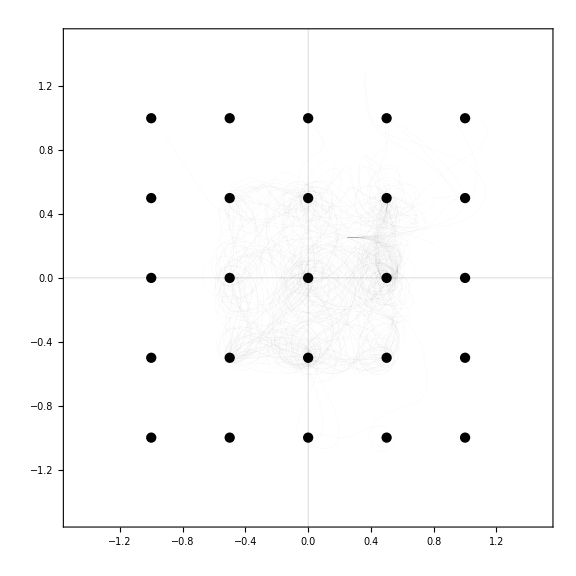

```mathematica
tmax=5;
sol=ParametricNDSolve[{{x''[t],y''[t]}==Sum[ζ/(Norm[gravPoints[[i]]-{x[t],y[t]}]^2)*Normalize[gravPoints[[i]]-{x[t],y[t]}],{i,1,n}],{x[0],y[0]}=={0.25,0.25},{x'[0],y'[0]}=={2,0.2}},{x[t],y[t]},{t,0,tmax},{ζ}];
xp=(x[t]/.sol);
yp=(y[t]/.sol);
Show[gravImg,Table[ParametricPlot[{xp[ζ]/.t->T,yp[ζ]/.t->T},{T,0,tmax},PlotStyle->{Opacity[0.1,Black],Thickness[0.0001]}],{ζ,0.2,5,1/5}]]
```

```mathematica
imgs=Table[Show[gravImg,Table[ParametricPlot[{xp[ζ]/.t->T,yp[ζ]/.t->T},{T,0,cT},PlotStyle->{Opacity[0.1,Black],Thickness[0.0001]}],{ζ,0.2,5,1/20}]],{cT,1/40,tmax,1/40}];
```

```mathematica
Export[NotebookDirectory[]<>"parametricGravityGrid.gif",imgs,"DisplayDurations"->0.1]
```

C:\Users\Julien\Desktop\Science Animations\ParametricGravitationalGrid\parametricGravityGrid.gif

```mathematica
EmitSound[Play[Sin[t*8000],{t,0,1}]]
```